```mathematica
SetDirectory["/Users/Jenna/Research/Cuba-3.0"]
```

/Users/Jenna/Research/Cuba-3.0

```mathematica
Install["Suave"]
```

LinkObject[/Users/Jenna/Research/Cuba-3.0/Suave,23275,15]

```mathematica
Clear[λ];
λ[r_,μ_]:=1+r^2-2*r*μ;
mp0=Import["/Users/Jenna/Research/DataFiles/test_matterPower_0.dat","Table"];
```

```mathematica
size=Dimensions[mp0][[1]]
α=Log[mp0[[2,1]]/mp0[[1,1]]]/Log[mp0[[2,2]]/mp0[[1,2]]]
β=Log[mp0[[size,2]]/mp0[[size-1,2]]]/Log[mp0[[size,1]]/mp0[[size-1,1]]]
```

496

1.03608

-2.44708

```mathematica
Pm=Interpolation[mp0]
```

InterpolatingFunction[{{0.0001,1.993}},<>]

```mathematica
Pmgood[k_]=If[k<0.0001||k>1.993,0,Pm[k]]
```

If[k<0.0001||k>1.993,0,Pm[k]]

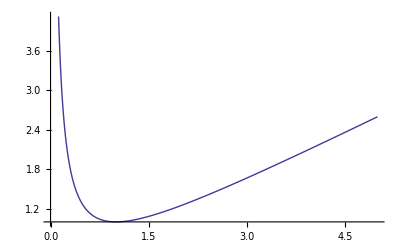

```mathematica
Plot[(1+r^2)/(2r),{r,0,5}]
```

```mathematica
Limit[(3r+7μ-10r*μ^2)/(1+r^2-2r*μ),r->1]
```

3/2+5 μ

```mathematica
f[r_,μ_]:=If[r==1&&μ==1,13/2,(3r+7μ-10r*μ^2)/(1+r^2-2r*μ)]
```

```mathematica
Clear[r,μ]
```

```mathematica
(* 2 fgps terms for first integral:
```

```mathematica
Clear[fgps];
fgps[k_] := Module[{r,μ},Suave[(r/14*Pmgood[k*r]*Pmgood[k*λ[r,μ]^(1/2)]*f[r,μ]),{r,0,1},{μ,-1,1},Verbose->0][[1,1]]];
```

```mathematica
fgps2[k_] := Module[{r,μ},Suave[(1/(14*r)*Pmgood[k/r]*Pmgood[k*λ[1/r,μ]^(1/2)]*f[1/r,μ]),{r,0,1},{μ,-1,1},Verbose->0][[1,1]]]
```

```mathematica
Clear[S]
S=fgps/@Take[mp0,{1,496,20}][[All,1]]-fgps2/@Take[mp0,{1,496,20}][[All,1]]
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

{910849.,1.33411×10^6,1.94589×10^6,2.78961×10^6,3.92987×10^6,5.29425×10^6,7.05091×10^6,8.76731×10^6,1.01905×10^7,1.14905×10^7,1.40773×10^7,2.20418×10^7,4.24968×10^7,7.48556×10^7,9.31008×10^7,7.19657×10^7,4.30918×10^7,2.34631×10^7,9.49408×10^6,3.25489×10^6,943241.,239105.,54061.4,11094.5,2116.86}

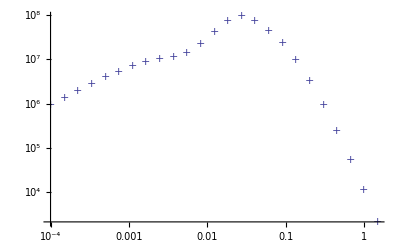

```mathematica
ListLogLogPlot[Thread[{Take[mp0[[All,1]],{1,496,20}],S}],PlotMarkers->"+"]
```